# 2D First-Passage time

## Drift towards the equilibrium at (x, xh) = (0, 0) with an absorbing boundary at xh=1. Initial condition is a wide distribution which narrows on approach to the fixed point.

## Write down the nondimensionalized Fokker-Planck equation

```mathematica
FP=λ*D[xh*P[x, xh], x]+D[xh*P[x, xh], xh]-κ*D[x*P[x, xh],xh]+λ*0.5*D[P[ x, xh],{x,2}]+0.5*D[P[x, xh],{xh,2}]
```

P[x,xh]+xh P^(0,1)[x,xh]-x κ P^(0,1)[x,xh]+0.5 P^(0,2)[x,xh]+xh λ P^(1,0)[x,xh]+0.5 λ P^(2,0)[x,xh]

## Choose the parameter values

```mathematica
λs = {0.02, 0.05, 0.1,0.2, 0.5};
κs = {0.1, 0.2,0.5, 1, 2};
params = Flatten[Table[{λ->l, κ->k}, {l, λs}, {k, κs}], 1]
legend =  Flatten[Table["λ="<>ToString[l]<>"; "<> "κ="<>ToString[k], {l, λs},{k, κs}], 1];
```

{{λ→0.02,κ→0.1},{λ→0.02,κ→0.2},{λ→0.02,κ→0.5},{λ→0.02,κ→1},{λ→0.02,κ→2},{λ→0.05,κ→0.1},{λ→0.05,κ→0.2},{λ→0.05,κ→0.5},{λ→0.05,κ→1},{λ→0.05,κ→2},{λ→0.1,κ→0.1},{λ→0.1,κ→0.2},{λ→0.1,κ→0.5},{λ→0.1,κ→1},{λ→0.1,κ→2},{λ→0.2,κ→0.1},{λ→0.2,κ→0.2},{λ→0.2,κ→0.5},{λ→0.2,κ→1},{λ→0.2,κ→2},{λ→0.5,κ→0.1},{λ→0.5,κ→0.2},{λ→0.5,κ→0.5},{λ→0.5,κ→1},{λ→0.5,κ→2}}

## Set up the mesh, boundary conditions, and initial condition

#### Choose the same initial width for every parameter set: the one with the largest s.s. width in x

```mathematica
Table[1/(2κ)+((1+κ) λ)/(2κ)/.p, {p, params}]
```

{5.11,2.56,1.03,0.52,0.265,5.275,2.65,1.075,0.55,0.2875,5.55,2.8,1.15,0.6,0.325,6.1,3.1,1.3,0.7,0.4,7.75,4.,1.75,1.,0.625}

```mathematica
{{1/(2κ)+((1+κ) λ)/(2κ),1/2},{1/2,(1+κ)/2}}/.params[[21]]
```

{{7.75,1/2},{1/2,0.55}}

#### Boundary condition at x*=1, y* = 2k/(1+Sqrt(1-4*l*k))

#### Also choose initial width for the steady-state width of each parameter pair

```mathematica
ystars = Table[Re[2*κ/(1+Sqrt[1-4*κ*λ])]/.p, {p, params}]
```

{0.100201,0.200806,0.505103,1.02084,2.08712,0.100505,0.202041,0.513167,1.05573,2.25403,0.101021,0.204168,0.527864,1.12702,2.76393,0.102084,0.208712,0.563508,1.38197,2.5,0.105573,0.225403,1.,1.,1.}

```mathematica
xf=15;
icPos = {5, 5};
icVar = {{1/(2κ)+((1+κ) λ)/(2κ),1/2},{1/2,(1+κ)/2}}/.params[[21]] 
ic0 = N[Table[PDF[MultinormalDistribution[icPos,icVar], {x, xh}], {i, params}]];(*ic0 : Choose widest s.s. distribution of the parameter values*)
icSS = N[Table[PDF[MultinormalDistribution[icPos,{{1/(2κ)+((1+κ) λ)/(2κ),1/2},{1/2,(1+κ)/2}}/.p], {x, xh}], {p, params}]];
(*icSS : Choose s.s. distribution width for each of the parameter values*)
bcs = Table[{P[-xf, xh]==0,
           P[xf, xh]==0,
           P[x, xf]==0,
           P[x, ystar]==0
}, {ystar,ystars}]

Needs["NDSolve`FEM`"]
meshes=Table[ToElementMesh[Rectangle[{-xf, ystar}, {xf, xf}],MaxCellMeasure->0.01 ], {ystar, ystars}]
mesh["Wireframe"]
```

{{7.75,1/2},{1/2,0.55}}

{{P[-15,xh]==0,P[15,xh]==0,P[x,15]==0,P[x,0.100201]==0},{P[-15,xh]==0,P[15,xh]==0,P[x,15]==0,P[x,0.200806]==0},{P[-15,xh]==0,P[15,xh]==0,P[x,15]==0,P[x,0.505103]==0},{P[-15,xh]==0,P[15,xh]==0,P[x,15]==0,P[x,1.02084]==0},{P[-15,xh]==0,P[15,xh]==0,P[x,15]==0,P[x,2.08712]==0},{P[-15,xh]==0,P[15,xh]==0,P[x,15]==0,P[x,0.100505]==0},{P[-15,xh]==0,P[15,xh]==0,P[x,15]==0,P[x,0.202041]==0},{P[-15,xh]==0,P[15,xh]==0,P[x,15]==0,P[x,0.513167]==0},{P[-15,xh]==0,P[15,xh]==0,P[x,15]==0,P[x,1.05573]==0},{P[-15,xh]==0,P[15,xh]==0,P[x,15]==0,P[x,2.25403]==0},{P[-15,xh]==0,P[15,xh]==0,P[x,15]==0,P[x,0.101021]==0},{P[-15,xh]==0,P[15,xh]==0,P[x,15]==0,P[x,0.204168]==0},{P[-15,xh]==0,P[15,xh]==0,P[x,15]==0,P[x,0.527864]==0},{P[-15,xh]==0,P[15,xh]==0,P[x,15]==0,P[x,1.12702]==0},{P[-15,xh]==0,P[15,xh]==0,P[x,15]==0,P[x,2.76393]==0},{P[-15,xh]==0,P[15,xh]==0,P[x,15]==0,P[x,0.102084]==0},{P[-15,xh]==0,P[15,xh]==0,P[x,15]==0,P[x,0.208712]==0},{P[-15,xh]==0,P[15,xh]==0,P[x,15]==0,P[x,0.563508]==0},{P[-15,xh]==0,P[15,xh]==0,P[x,15]==0,P[x,1.38197]==0},{P[-15,xh]==0,P[15,xh]==0,P[x,15]==0,P[x,2.5]==0},{P[-15,xh]==0,P[15,xh]==0,P[x,15]==0,P[x,0.105573]==0},{P[-15,xh]==0,P[15,xh]==0,P[x,15]==0,P[x,0.225403]==0},{P[-15,xh]==0,P[15,xh]==0,P[x,15]==0,P[x,1.]==0},{P[-15,xh]==0,P[15,xh]==0,P[x,15]==0,P[x,1.]==0},{P[-15,xh]==0,P[15,xh]==0,P[x,15]==0,P[x,1.]==0}}

{ElementMesh[{{-15.,15.},{0.100201,15.}},{QuadElement[<44700>]}],ElementMesh[{{-15.,15.},{0.200806,15.}},{QuadElement[<44400>]}],ElementMesh[{{-15.,15.},{0.505103,15.}},{QuadElement[<43500>]}],ElementMesh[{{-15.,15.},{1.02084,15.}},{QuadElement[<42000>]}],ElementMesh[{{-15.,15.},{2.08712,15.}},{QuadElement[<39000>]}],ElementMesh[{{-15.,15.},{0.100505,15.}},{QuadElement[<44700>]}],ElementMesh[{{-15.,15.},{0.202041,15.}},{QuadElement[<44400>]}],ElementMesh[{{-15.,15.},{0.513167,15.}},{QuadElement[<43500>]}],ElementMesh[{{-15.,15.},{1.05573,15.}},{QuadElement[<42000>]}],ElementMesh[{{-15.,15.},{2.25403,15.}},{QuadElement[<38400>]}],ElementMesh[{{-15.,15.},{0.101021,15.}},{QuadElement[<44700>]}],ElementMesh[{{-15.,15.},{0.204168,15.}},{QuadElement[<44400>]}],ElementMesh[{{-15.,15.},{0.527864,15.}},{QuadElement[<43500>]}],ElementMesh[{{-15.,15.},{1.12702,15.}},{QuadElement[<41700>]}],ElementMesh[{{-15.,15.},{2.76393,15.}},{QuadElement[<36900>]}],ElementMesh[{{-15.,15.},{0.102084,15.}},{QuadElement[<44700>]}],ElementMesh[{{-15.,15.},{0.208712,15.}},{QuadElement[<44400>]}],ElementMesh[{{-15.,15.},{0.563508,15.}},{QuadElement[<43500>]}],ElementMesh[{{-15.,15.},{1.38197,15.}},{QuadElement[<41100>]}],ElementMesh[{{-15.,15.},{2.5,15.}},{QuadElement[<37500>]}],ElementMesh[{{-15.,15.},{0.105573,15.}},{QuadElement[<44700>]}],ElementMesh[{{-15.,15.},{0.225403,15.}},{QuadElement[<44400>]}],ElementMesh[{{-15.,15.},{1.,15.}},{QuadElement[<42000>]}],ElementMesh[{{-15.,15.},{1.,15.}},{QuadElement[<42000>]}],ElementMesh[{{-15.,15.},{1.,15.}},{QuadElement[<42000>]}]}

mesh[Wireframe]

## Calculate the probability distribution and the flux through the boundary

```mathematica
NDSolverParams[param_, ic_, bc_, mesh_] :=Module[{N},
N = NDSolve[Join[{(FP/. param)==-ic}, bc],
                                   P,Element[{x, xh}, mesh], 
Method->"FiniteElement"];
Return[(P/.N[[1]])];
]
```

```mathematica
solsSS=MapThread[NDSolverParams, {params, icSS, bcs, meshes}];
solsIc0=MapThread[NDSolverParams, {params, ic0, bcs, meshes}];
```

```mathematica
fluxSS = Table[Derivative[0,1][sol],{sol, solsSS}];
fluxIc0 = Table[Derivative[0,1][sol],{sol, solsIc0}];
```

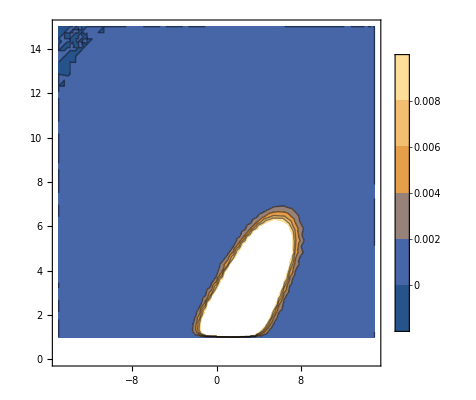

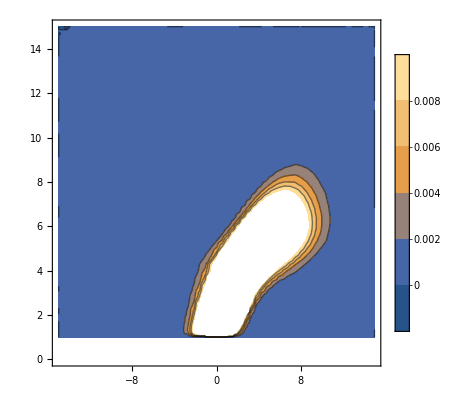

```mathematica
cSS =ContourPlot[solsSS[[23]][x, xh], {x, -xf, xf}, {xh, 0, xf}, PlotLegends->Automatic, PlotRange->{-0.01, 0.01}];
cIc0 =ContourPlot[solsIc0[[24]][x, xh], {x, -xf, xf}, {xh, 0, xf}, PlotLegends->Automatic, PlotRange->{-0.01, 0.01}];
Show[cSS]
Show[cIc0]
```

```mathematica
XSS = MapThread[#1[x,#2]&,{fluxSS,ystars}];
XIc0 =MapThread[#1[x,#2]&,{fluxIc0,ystars}];
```

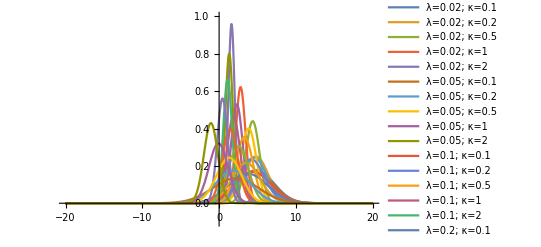

```mathematica
Plot[XSS, {x, -xf, xf}, PlotRange->{-0.1, 1}, PlotLegends->legend]
```

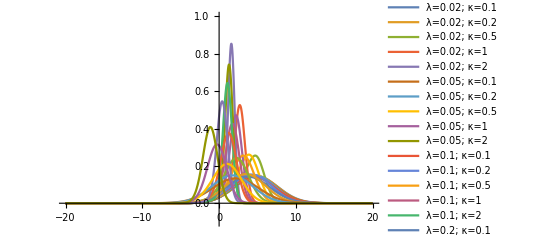

```mathematica
Plot[XIc0, {x, -xf, xf}, PlotRange->{-0.1, 1}, PlotLegends->legend]
```

```mathematica
normsSS = Table[NIntegrate[xp, {x, -10, 15}, WorkingPrecision->10], {xp, XSS}]
meansSS= Table[NIntegrate[xp*x, {x, -10, 15}, WorkingPrecision->10], {xp, XSS}]
secondSS = Table[NIntegrate[xp*x*x, {x, -10, 15}, WorkingPrecision->10], {xp, XSS}];
varsSS= secondSS-meansSS^2
diffSS = varsSS/meansSS;
```

{2.005776901,2.002899283,1.992262608,1.994583353,1.983360187,2.005841572,2.003456865,1.99707618,1.999964892,1.978183355,2.005929327,2.004151254,2.000709233,2.002756091,1.931744244,2.006036172,2.005021405,2.003637303,2.00268523,1.945330491,2.00580233,2.005697248,2.002612255,1.994351651,1.953260755}

{9.755239036,9.583833137,7.668173794,4.541181039,2.835958739,9.356196291,9.013284736,6.653629462,3.835678289,2.407066575,8.709877135,8.169048482,5.634026185,3.193351994,2.115411928,7.477392166,6.720121799,4.297700989,2.536035498,0.9348498576,4.135153143,3.300024871,2.267714457,-0.1571870081,-1.903222598}

{-37.5828806,-41.1811835,-28.2819478,-9.85580719,-3.79139667,-33.5674041,-35.9540447,-20.8558614,-6.77427694,-2.58176062,-27.3429031,-28.5991208,-14.3195451,-4.35572847,-1.7198153,-16.4718771,-17.3126326,-7.25906367,-2.21705917,0.14276315,6.04663267,1.7083062,0.36778842,1.51344253,-0.89117227}

```mathematica
normsIc0 = Table[NIntegrate[xp, {x, -10, 15}, WorkingPrecision->10], {xp, XIc0}]
meansIc0= Table[NIntegrate[xp*x, {x, -10, 15}, WorkingPrecision->10], {xp, XIc0}]
secondIc0 = Table[NIntegrate[xp*x*x, {x, -10, 15}, WorkingPrecision->10], {xp, XIc0}];
varsIc0 = secondIc0-meansIc0^2
diffIc0 = varsIc0/meansIc0;
```

{2.005177563,2.001231768,1.9938288,1.994834049,1.663805914,2.005261658,2.002064858,1.99782459,1.99940202,1.778251126,2.005400871,2.002969284,2.000660351,2.001395154,1.864109595,2.005606619,2.004023403,2.002717904,2.000198941,1.92930457,2.00580233,2.004894043,2.000115582,1.990518985,1.941844592}

{9.74230466,9.427121767,6.55599293,3.984057979,2.095535408,9.338421734,8.787442962,5.666845443,3.341237958,1.905783282,8.6875852,7.901402142,4.757995521,2.723377681,1.793906952,7.453858661,6.443514804,3.541680177,2.03308071,0.7238707555,4.135153143,3.090137567,1.674499153,-0.5840056555,-2.123724917}

{-32.3182065,-30.996043,-17.0978347,-6.40781144,-1.0762508,-28.7355282,-26.3958677,-12.1981601,-4.13073794,-0.91223902,-23.1914249,-20.0055829,-7.65176072,-2.22773125,-0.75002663,-13.551835,-10.332353,-2.5435059,-0.42598496,0.49462726,6.04663267,5.59832941,3.19812142,1.67602592,-1.1071459}

```mathematica
grid = Flatten[Table[{l, s}, {l, λs}, {s, κs}], 1];
params
```

{{λ→0.02,κ→0.1},{λ→0.02,κ→0.2},{λ→0.02,κ→0.5},{λ→0.02,κ→1},{λ→0.02,κ→2},{λ→0.05,κ→0.1},{λ→0.05,κ→0.2},{λ→0.05,κ→0.5},{λ→0.05,κ→1},{λ→0.05,κ→2},{λ→0.1,κ→0.1},{λ→0.1,κ→0.2},{λ→0.1,κ→0.5},{λ→0.1,κ→1},{λ→0.1,κ→2},{λ→0.2,κ→0.1},{λ→0.2,κ→0.2},{λ→0.2,κ→0.5},{λ→0.2,κ→1},{λ→0.2,κ→2},{λ→0.5,κ→0.1},{λ→0.5,κ→0.2},{λ→0.5,κ→0.5},{λ→0.5,κ→1},{λ→0.5,κ→2}}

```mathematica
normArraySS = ArrayReshape[normsSS, {5, 5}];
varArraySS = ArrayReshape[varsSS, {5, 5}];
meanArraySS = ArrayReshape[meansSS, {5, 5}];
diffArraySS = ArrayReshape[diffSS, {5, 5}];
normArrayIc0 = ArrayReshape[normsIc0, {5, 5}];
varArrayIc0 = ArrayReshape[varsIc0, {5, 5}];
meanArrayIc0 = ArrayReshape[meansIc0, {5, 5}];
diffArrayIc0 = ArrayReshape[diffIc0, {5, 5}];
```

```mathematica
cf[x_]:=Blend[{{-2, Red},{ 1,White},{5,Blue}}, x]
```

```mathematica
xticks = Transpose[{{1, 2, 3, 4, 5}, λs}];
yticks = Transpose[{{1, 2, 3, 4, 5}, κs}];
```

```mathematica
ArrayPlot[varArraySS, ColorFunction->(Blend[{{-1, Red},{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"var(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]

ArrayPlot[ArrayReshape[Table[Blend[{{-2, Red},{ 0,White},{5,Blue}}, i],{i,Flatten[meanArraySS]}], {5,5}], PlotLegends->{Placed[BarLegend[{cf[#]&,{-2, 5}},LegendLabel->"mean(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]

ArrayPlot[normArraySS, ColorFunction->(Blend[{White,Blue},#]&), PlotLegends->{Placed[BarLegend[Automatic,Automatic,LegendLabel->"norm(e(x))"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
ArrayPlot[varArrayIc0, ColorFunction->(Blend[{{-1, Red},{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"var(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]

ArrayPlot[ArrayReshape[Table[Blend[{{-2, Red},{ 0,White},{5,Blue}}, i],{i,Flatten[meanArrayIc0]}], {5,5}], PlotLegends->{Placed[BarLegend[{cf[#]&,{-2, 5}},LegendLabel->"mean(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]

ArrayPlot[normArrayIc0, ColorFunction->(Blend[{White,Blue},#]&), PlotLegends->{Placed[BarLegend[Automatic,Automatic,LegendLabel->"norm(e(x))"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]
```

-Graphics-

-Graphics-

-Graphics-